```mathematica
$Assumptions = {Δ ∈ Reals,Δ < 0, t ∈ Reals, ϕ ∈ Reals, θ ∈ Reals, z ∈ Integers, q ∈ Reals}
```

{Δ∈ℝ,Δ<0,t∈ℝ,ϕ∈ℝ,θ∈ℝ,z∈ℤ,q∈ℝ}

```mathematica
α = I t
```

ⅈ t

```mathematica
ϕ = 0
```

0

```mathematica
ϵ =FullSimplify[Sqrt[6]*q*Im[α]]
```

√6 q t

```mathematica
Δt = FullSimplify[3/2 Δ]
```

(3 Δ)/2

```mathematica
ϵp =FullSimplify[ Δt/Sqrt[2]+(ϵ+Sqrt[ϵ^2+Δt^2])/Sqrt[2]]
```

1/4 (4 √3 q t+3 √2 Δ+√6 √(8 q^2 t^2+3 Δ^2))

```mathematica
ϵm = FullSimplify[ Δt/Sqrt[2]-(ϵ+Sqrt[ϵ^2+Δt^2])/Sqrt[2]]
```

1/4 (-4 √3 q t+3 √2 Δ-√6 √(8 q^2 t^2+3 Δ^2))

```mathematica
C1m =FullSimplify[ 1/Sqrt[2 * Sqrt[ϵ^2+Δt^2]*(ϵ + Sqrt[ϵ^2+Δt^2])] 1/Sqrt[3](2 I Exp[I ϕ] ϵp Sin[θ]-ϵm)]
```

(2 √6 q t-3 Δ+√(24 q^2 t^2+9 Δ^2)+2 ⅈ (2 √6 q t+3 Δ+√(24 q^2 t^2+9 Δ^2)) Sin[θ])/(6 √(3 Δ^2+2 q t (4 q t+√(16 q^2 t^2+6 Δ^2))))

```mathematica
C3m =FullSimplify[ 1/Sqrt[2 * Sqrt[ϵ^2+Δt^2]*(ϵ + Sqrt[ϵ^2+Δt^2])] 1/Sqrt[3](2 I Exp[I ϕ] ϵp Sin[θ - 2 π/3]-ϵm)]
```

(4 √3 q t-3 √2 Δ+√6 √(8 q^2 t^2+3 Δ^2)-2 ⅈ (4 √3 q t+3 √2 Δ+√6 √(8 q^2 t^2+3 Δ^2)) Cos[π/6-θ])/(6 √(6 Δ^2+4 q t (4 q t+√(16 q^2 t^2+6 Δ^2))))

```mathematica
C5m =FullSimplify[ 1/Sqrt[2 * Sqrt[ϵ^2+Δt^2]*(ϵ + Sqrt[ϵ^2+Δt^2])] 1/Sqrt[3](2 I Exp[I ϕ] ϵp Sin[θ +2 π/3]-ϵm)]
```

(4 √3 q t-3 √2 Δ+√6 √(8 q^2 t^2+3 Δ^2)+2 ⅈ (4 √3 q t+3 √2 Δ+√6 √(8 q^2 t^2+3 Δ^2)) Cos[π/6+θ])/(6 √(6 Δ^2+4 q t (4 q t+√(16 q^2 t^2+6 Δ^2))))

```mathematica
(*α = I * 5
Δ = -100*)
```

```mathematica
(*t1q = FullSimplify[Conjugate[C1m] * D[C1m, q]]
t1θ = FullSimplify[1/q Conjugate[C1m] * D[C1m, θ]]*)
```

```mathematica
(*O1 = FullSimplify[1/q D[t1θ * q, q] - 1/q D[t1q, θ]]*)
```

```mathematica
(*t3q = FullSimplify[Conjugate[C3m] * D[C3m, q]]
t3θ = FullSimplify[1/q Conjugate[C3m] * D[C3m, θ]]*)
```

```mathematica
(*O3 =  FullSimplify[1/q D[t3θ * q, q] - 1/q D[t3q, θ]]*)
```

```mathematica
(*t5q = FullSimplify[Conjugate[C5m] * D[C5m, q]]
t5θ = FullSimplify[1/q Conjugate[C5m] * D[C5m, θ]]*)
```

```mathematica
(*O5 =  FullSimplify[1/q D[t5θ * q, q] - 1/q D[t5q, θ]]*)
```

```mathematica
(*FullSimplify[O1 + O3 + O5]*)
```

```mathematica
(*FullSimplify[-2/q * Im[Conjugate[D[C1m,q]] * D[C1m,θ]] + -2/q * Im[Conjugate[D[C3m,q]] * D[C3m,θ]] + -2/q * Im[Conjugate[D[C5m,q]] * D[C5m,θ]]]*)
```

```mathematica
(*Clear[α, Δ]*)
```

```mathematica
Series[FullSimplify[Conjugate[C1m]*C1m], {q, 0, 2}]
```

1/3+(2 (-t^2+4 t^2 Sin[θ]^2) q^2)/(9 Δ^2)+O[q]^3

```mathematica
Series[FullSimplify[Conjugate[C1m]*C1m], {q, 0, 2}]
```

1/3+(2 (-t^2+4 t^2 Sin[θ]^2) q^2)/(9 Δ^2)+O[q]^3

```mathematica
Series[FullSimplify[Conjugate[C3m]*C3m], {q, 0, 2}]
```

1/3+(2 (t^2+2 t^2 Sin[π/6+2 θ]) q^2)/(9 Δ^2)+O[q]^3

```mathematica
Series[FullSimplify[Conjugate[C5m]*C5m], {q, 0, 2}]
```

1/3+(2 (t^2+2 t^2 Cos[1/3 (π+6 θ)]) q^2)/(9 Δ^2)+O[q]^3

```mathematica
H = FullSimplify[{{Sqrt[6] Im[α] + Δ/2, 0, 3 Δ/2}, {0, -Δ, 0}, {3 Δ/2, 0, -Sqrt[6] Im[α] + Δ/2}}]
```

{{√6 t+Δ/2,0,(3 Δ)/2},{0,-Δ,0},{(3 Δ)/2,0,1/2 (-2 √6 t+Δ)}}

```mathematica
q = 1
Δ = -1
t =3
```

1

-1

3

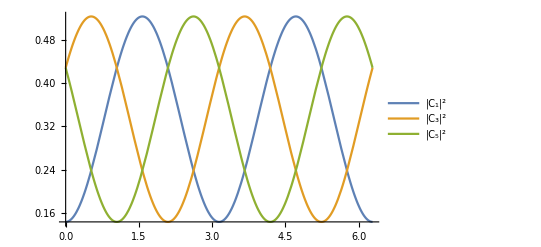

```mathematica
Plot[{5/7*C1m*Conjugate[C1m], 5/7*C3m * Conjugate[C3m], 5/7*C5m * Conjugate[C5m]}, {θ, 0, 2 π}, PlotLegends->{"|C_1|^2","|C_3|^2", "|C_5|^2" }]
```

```mathematica
FullSimplify[C1m*Conjugate[C1m] + C3m*Conjugate[C3m] + C5m*Conjugate[C5m]]
```

7/5

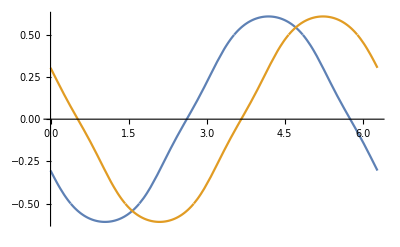

```mathematica
Plot[{Arg[C3m/C1m]*1/π,Arg[C5m/C1m]*1/π}, {θ, 0, 2 π}]
```